```mathematica
sbox="E4D12FB83A6C5907"
sbox=PRESENTsbox="C56B90AD3EF84712"
sbox=MIDORIsbox0="cad3ebf789150246"
sbox=MIDORIsbox1="1053e2f7da9bc846"

permutation={1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

l=4;m=4;Nr=4;
ClearAll[S]
S[x_]:=S[x]=IntegerDigits[FromDigits[sbox,16],16,16][[x+1]]
```

```mathematica
(*  istruzione per contare il numero di 1 nel binario dell'intero 11 in base 2 *)
DigitCount[11,2,1]
```

```mathematica
ClearAll[LAT,T,DDT,DDT2]
T[f_,a_,b_][x_]:=(-1)^(DigitCount[BitAnd[a,x],2,1]+DigitCount[BitAnd[b,f[x]],2,1])

n=4
dom=Range[0,2^n-1]
LAT[f_]:=Table[Plus@@Map[T[f,a,b],dom]/2^(n+1),{a,0,2^n-1},{b,0,2^n-1}]
Without0[matrix_]:=Transpose[Drop[Transpose[Drop[matrix,1]],1]]
```

```mathematica
ArrayPlot[LAT[S],ColorFunction->"TemperatureMap"]
```

```mathematica
ArrayPlot[Transpose[Drop[Transpose[Drop[LAT[S],1]],1]],ColorFunction->"TemperatureMap"]
```

```mathematica
LAT[S]//TableForm
```

```mathematica
dom=Range[0,2^n-1]

RowDDT[f_,dx_]:=Map[(BitXor[f[BitXor[#,dx]],f[#]])&,dom]
RowDDT2[f_,dx_]:=Map[{dx+1,#[[1]]+1}->#[[2]]&,Tally[RowDDT[f,dx]]]
```

```mathematica
ClearAll[DDT]
sparseDDT[f_]:=Flatten@Map[RowDDT2[f,#]&,dom]
DDT[f_]:=Normal[SparseArray[sparseDDT[f]]]
DDT[S]/2^n//MatrixForm
difference=Max[mm=Drop[DDT[S],1]]
ArrayPlot[mm,ColorFunction->"TemperatureMap"]
```

```mathematica
characteristics=sparseDDT[S]
```

```mathematica
(*DDT[f_]:=Map[RowDDT[S,#]&,Range[0,2^n-1]]*)
DDT[S]//TableForm
```

```mathematica
RowDDT[S,3]
```

```mathematica
LAT[S]//TableForm
```

```mathematica
char=characteristics[[3]]
dx=char[[1,1]]
dy=char[[1,2]]
weigth=char[[2]]
indexes=Flatten@Position[IntegerDigits[dy,2,n],1]
box=2
(* permuto gli indici *)
pindexes=Map[{box,#}&,indexes]

edges=DirectedEdge[{dx,box},pindexes,weigth]
```

```mathematica
DeltaY[indices_]:=Select[Table[{Plus@@(2^(4-Map[First,Select[indices,#[[2]]==box&]])),box},{box,1,4}],#[[1]]=!=0&]

TargetNode[char1_,box1_]:=Module[{},
(
dx1=char1[[1,1]];
dy1=char1[[1,2]];
weigth1=char1[[2]];
indexes1=Flatten@Position[IntegerDigits[dy1,2,n],1];
(* permuto gli indici *)
pindexes1=Map[{box1,#}&,indexes1];

DirectedEdge[{{dx1,box1}},DeltaY[pindexes1],weigth1]
)]

TargetNode[char1_,box1_,char2_,box2_]:=Module[{},
(
dx1=char1[[1,1]];
dy1=char1[[1,2]];
weigth1=char1[[2]];
indexes1=Flatten@Position[IntegerDigits[dy1,2,n],1];
(* permuto gli indici *)
pindexes1=Map[{box1,#}&,indexes1];

dx2=char2[[1,1]];
dy2=char2[[1,2]];
weigth2=char2[[2]];
indexes2=Flatten@Position[IntegerDigits[dy2,2,n],1];
(* permuto gli indici --- specifico all'SPN del libro*)
pindexes2=Map[{box2,#}&,indexes2];


joinedindexes=Join[pindexes1,pindexes2];
DirectedEdge[{{dx1,box1},{dx2,box2}},DeltaY[joinedindexes],weigth1 weigth2/2^n]
)]
```

```mathematica
TargetNode[characteristics[[3]],2]
TargetNode[characteristics[[3]],2,characteristics[[7]],3]
```

```mathematica
MakeEdges[node_?(Length[#]===1&)]:=Module[{dx,box,edges},
(

(*Print["unario"];*)
{dx,box}=node[[1]];
edges=Map[TargetNode[#,box]&,Select[sparseDDT[S],#[[1,1]]==dx+1&]];
Select[edges,0<Length[#[[2]]]<=2&]
)]
```

```mathematica
MakeEdges[node_?(Length[#]===2&)]:=Module[{dx1,dx2,box1,box2,rowdx1,rowdx2,edges},
(
(*Print["binario"];*)
{{dx1,box1},{dx2,box2}}=node;
(* seleziono le caratteristiche non-nulle della differenza in ingresso dx *)
rowdx1=Select[sparseDDT[S],#[[1,1]]==dx1+1&];
rowdx2=Select[sparseDDT[S],#[[1,1]]==dx2+1&];
(* formo un arco tra la differenza in ingresso e ognuna delle differenze in uscita derivate dalle coppie di caratteristiche in entrata *)
edges=Map[TargetNode[#[[1]],box1,#[[2]],box2]&,Tuples[{rowdx1,rowdx2}]];

(*  seleziono quelle con solo 2 sbox attive in uscita *)
Select[edges,0<Length[#[[2]]]<=2&]
)]
```

```mathematica
MakeEdges[{{dx,box}}]
```

```mathematica
MakeEdges[{{dx,box},{dx+1,box+1}}]
```

```mathematica
V={};

newedges={};newnodes={};edges={};
PickNode[nodes_]:=Module[{i},
(
i=RandomInteger[{1,Length[Q]}];
(*Print[i];*)

{Q[[i]],Drop[Q,{i}]})
]
```

```mathematica
boxes=Range[1,4];
deltas=Range[0,2^n-1];
Q=Map[{#}&,Tuples[{deltas,boxes}]];Length[Q]
```

```mathematica
While[Length[Q]<300&&Length[Q]>0,
(
Print[Length[Q]];
{node,Q}=PickNode[Q];
(*Print["->",node];*)
V=Append[V,node];
newedges=MakeEdges[node];
Print[newedges];
newnodes=Complement[Map[#[[2]]&,newedges],V];
Q=Join[Q,newnodes];
edges=Union[Join[edges,newedges]];
(*Print[Graph[edges]]*)
)]
```

```mathematica
edges
```

```mathematica
cycles=FindCycle[edges,Infinity,All];

HighlightGraph[edges,cycles]
```

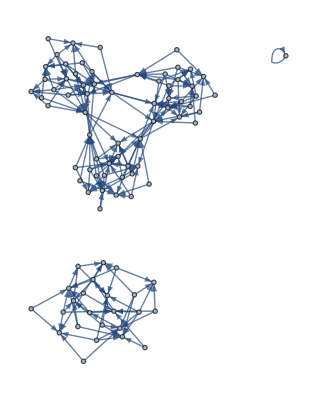

```mathematica
TableForm[V,TableDepth->1]
```